```mathematica
gcp = Compile[{{x}, {y}, {z}},16/N[Pi]^2*Sum[1/(n*m)*Exp[-N[Pi]*Sqrt[n^2+m^2]*x]*Sin[n*N[Pi]*y]*Sin[m*N[Pi]*z],{n, 1, 20,  2}, {m, 1,20, 2}]]
```

CompiledFunction[…]

```mathematica
Manipulate[DensityPlot[gcp[x, y, z], {y, 0, 1}, {z, 0, 1},PlotRange -> {0, 1},PlotRangeClipping -> False,ColorFunctionScaling -> False, ColorFunction -> (ColorData["DeepSeaColors"][#/1] &),  WorkingPrecision->2, PlotLegends->BarLegend[Automatic, LegendMarkerSize->{10, 300},LabelStyle->{FontSize->14, Black}]],{x, 0, 0.5, 0.05}]
```

```mathematica
Animate[DensityPlot[gcp[x, y, z], {y, 0, 1}, {z, 0, 1},PlotRange -> {0, 1},ColorFunctionScaling -> False, ColorFunction -> (ColorData["DeepSeaColors"][#/1] &),  WorkingPrecision->2, PlotLegends->BarLegend[Automatic, LegendMarkerSize->{10, 300},LabelStyle->{FontSize->14, Black}]],{x, 0, 0.2, 0.01}, AnimationRate->0.002]
```

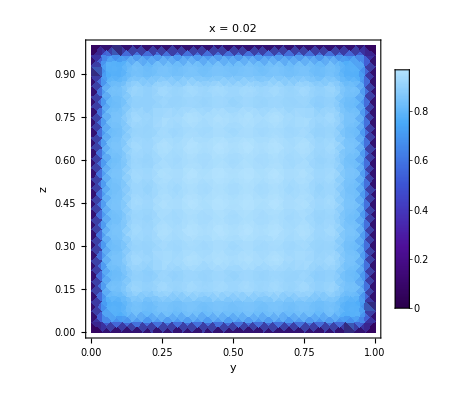
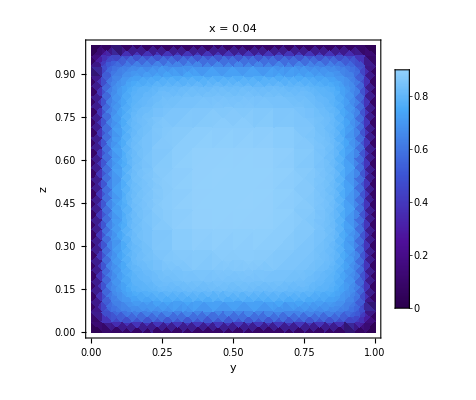
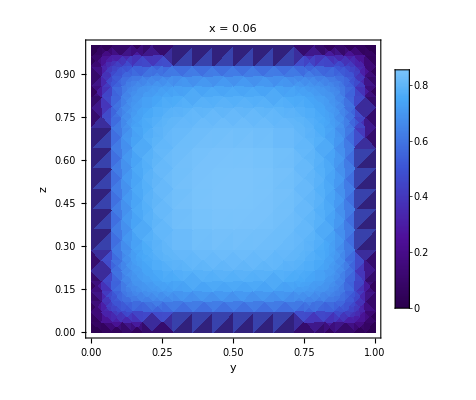
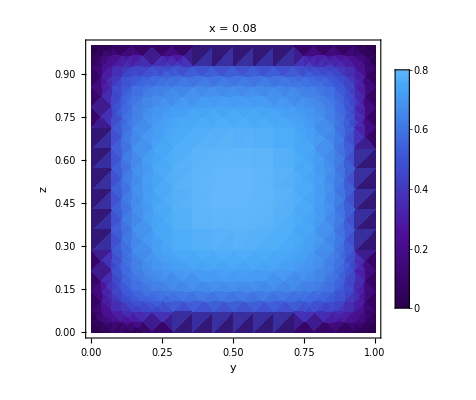
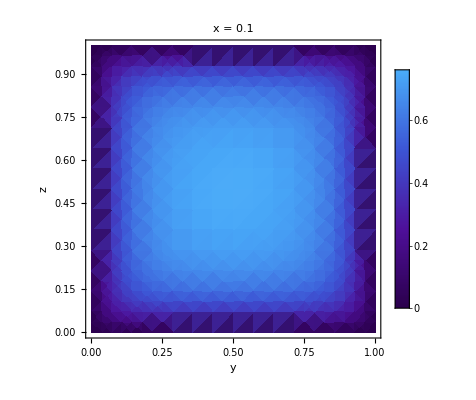
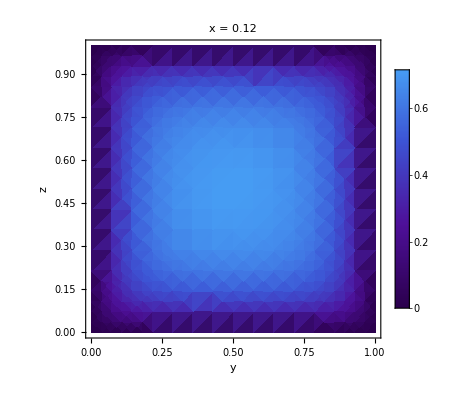
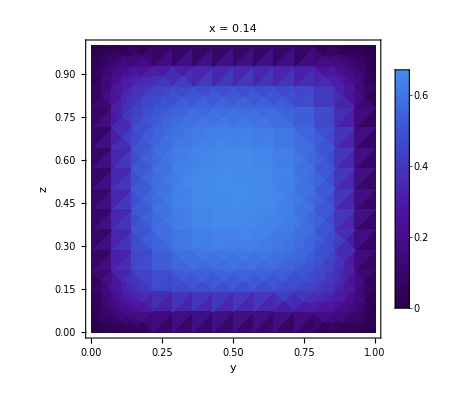
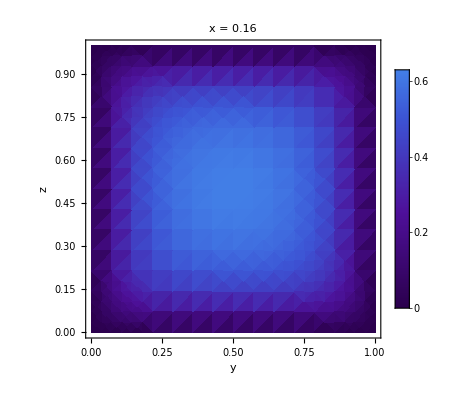

```mathematica
frames1 = Table[DensityPlot[gcp[x, y, z], {y, 0, 1}, {z, 0, 1}, WorkingPrecision->2, PlotRange -> {0, 1},PlotLegends->BarLegend[Automatic, LegendMarkerSize->{10, 300},LabelStyle->{FontSize->14, Black}],ColorFunctionScaling -> False, ColorFunction -> (ColorData["DeepSeaColors"][#/1] &), LabelStyle->Directive[Black], Frame->True,FrameLabel->{"y", Rotate["z", 80.1]}, PlotLabel->Row[{"x = ",x}]], {x, 0.02, 0.2, 0.02}]
```

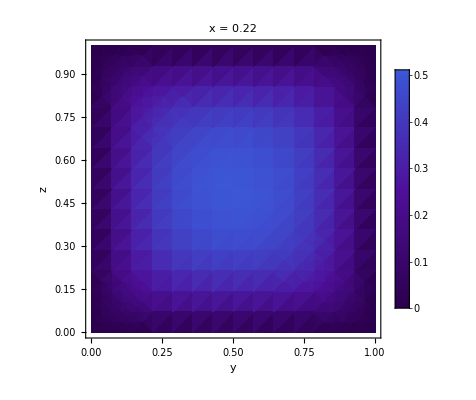
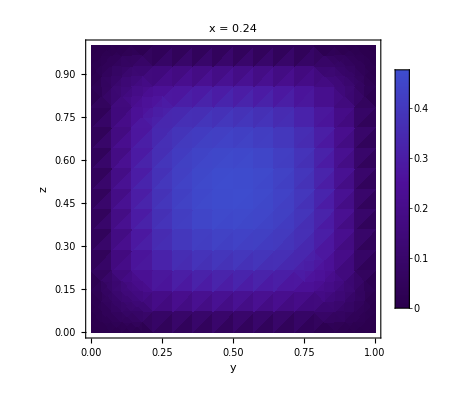
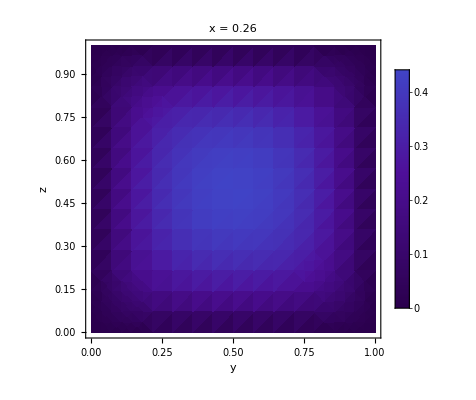
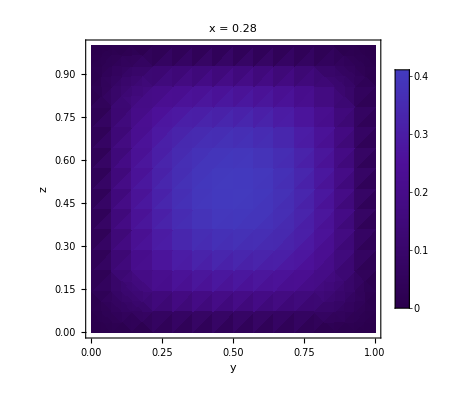
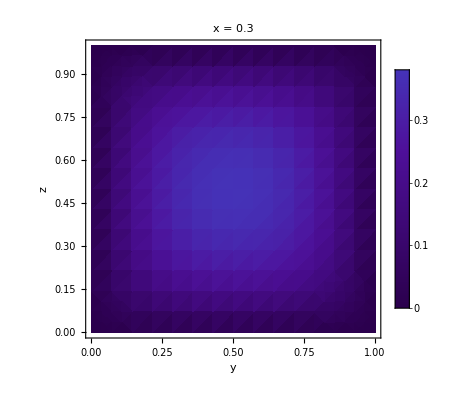
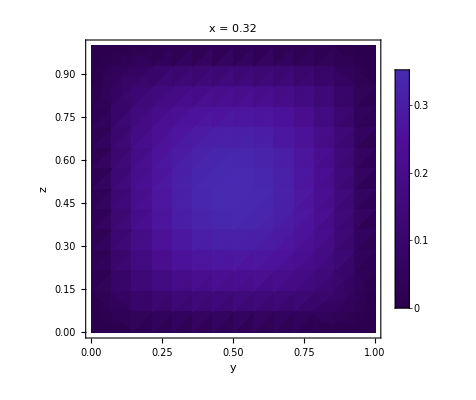
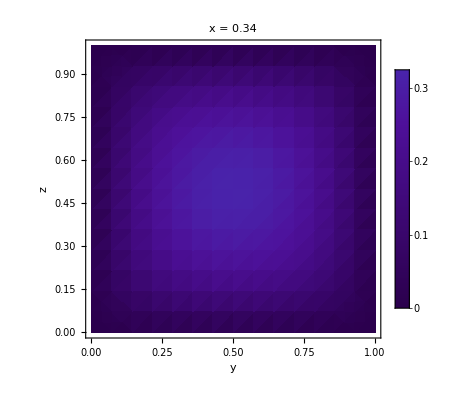
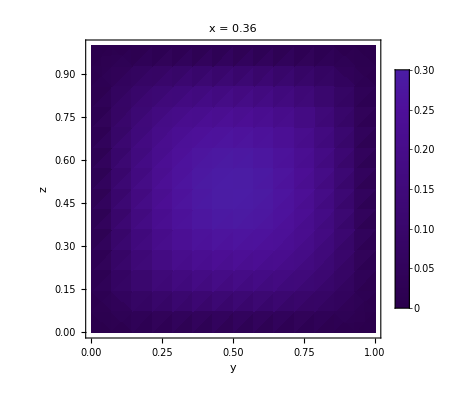

```mathematica
frames2 = Table[DensityPlot[gcp[x, y, z], {y, 0, 1}, {z, 0, 1}, WorkingPrecision->2, PlotRange -> {0, 1},PlotLegends->BarLegend[Automatic, LegendMarkerSize->{10, 300},LabelStyle->{FontSize->14, Black}],ColorFunctionScaling -> False, ColorFunction -> (ColorData["DeepSeaColors"][#/1] &), LabelStyle->Directive[Black], Frame->True,FrameLabel->{"y", Rotate["z", 80.1]}, PlotLabel->Row[{"x = ",x}]],{x, 0.22, 0.4, 0.02}]
```

```mathematica
frames = Join[frames1, frames2 ]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListAnimate[frames]
```

```mathematica
ListAnimate[frames]
```

```mathematica
Export["C:/Users/nafer/OneDrive/Documents/Física/Electromagnetismo/Electromagnetismo 1/WMathematica/Griffits_Example_3.5/animacion2d.gif", frames, "DisplayDurations"->0.5]
```

C:/Users/nafer/OneDrive/Documents/Física/Electromagnetismo/Electromagnetismo 1/WMathematica/animacion2d.gif

```mathematica
frames3d1 = Table[DensityPlot3D[gcp[x,y, z], {x, 0, a}, {y, 0, 1}, {z, 0, 1},   WorkingPrecision->2, PlotPoints->35, PlotRange -> {0, 1},AxesLabel->{x, y, z},  LabelStyle->Directive[Black], ColorFunction -> (ColorData["DeepSeaColors"][#/1] &), PlotLegends->BarLegend[Automatic, LegendMarkerSize->{10, 300},LabelStyle->{FontSize->14, Black}], PlotLabel->Row[{"x ∈ {0, ",a,"}" }]],{a, 0.02, 0.1, 0.02}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
frames3d2 = Table[DensityPlot3D[gcp[x,y, z], {x, 0, a}, {y, 0, 1}, {z, 0, 1},   WorkingPrecision->2, PlotPoints->35, PlotRange -> {0, 1},AxesLabel->{x, y, z},  LabelStyle->Directive[Black], ColorFunction -> (ColorData["DeepSeaColors"][#/1] &), PlotLegends->BarLegend[Automatic, LegendMarkerSize->{10, 300},LabelStyle->{FontSize->14, Black}],PlotLabel->Row[{"x ∈ {0, ",a,"}" }]],{a, 0.12, 0.2, 0.02}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
frames3d3 = Table[DensityPlot3D[gcp[x,y, z], {x, 0, a}, {y, 0, 1}, {z, 0, 1},   WorkingPrecision->2, PlotPoints->35, PlotRange -> {0, 1},AxesLabel->{x, y, z},  LabelStyle->Directive[Black], ColorFunction -> (ColorData["DeepSeaColors"][#/1] &), PlotLegends->BarLegend[Automatic, LegendMarkerSize->{10, 300},LabelStyle->{FontSize->14, Black}],PlotLabel->Row[{"x ∈ {0, ",a,"}" }]],{a, 0.22, 0.3, 0.02}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
frames3d4 = Table[DensityPlot3D[gcp[x,y, z], {x, 0, a}, {y, 0, 1}, {z, 0, 1},   WorkingPrecision->2, PlotPoints->35, PlotRange -> {0, 1},AxesLabel->{x, y, z},  LabelStyle->Directive[Black], ColorFunction -> (ColorData["DeepSeaColors"][#/1] &), PlotLegends->BarLegend[Automatic, LegendMarkerSize->{10, 300},LabelStyle->{FontSize->14, Black}], PlotLabel->Row[{"x ∈ {0, ",a,"}" }]],{a, 0.32, 0.4, 0.02}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
frames3d = Join[frames3d1, frames3d2, frames3d3,frames3d4]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ListAnimate[frames3d, 2]
```

```mathematica
Export["C:/Users/nafer/OneDrive/Documents/Física/Electromagnetismo/Electromagnetismo 1/WMathematica/Griffits_Example_3.5/animacion.gif", frames3d, "DisplayDurations"->0.5]
```

C:/Users/nafer/OneDrive/Documents/Física/Electromagnetismo/Electromagnetismo 1/WMathematica/animacion.gif

```mathematica
frames12 = Table[Plot3D[gcp[x, y, z], {y, 0, 1}, {z, 0, 1}, WorkingPrecision->2, PlotRange -> {0, 1},PlotLegends->BarLegend[Automatic, LegendMarkerSize->{10, 300},LabelStyle->{FontSize->14, Black}],AxesLabel->{"y", "z", "ϕ(y, z)"}, ColorFunction->"DeepSeaColors", LabelStyle->Directive[Black], PlotLabel->Row[{"x = ",x}]],{x, 0.02, 0.2, 0.02}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
frames22 = Table[Plot3D[gcp[x, y, z], {y, 0, 1}, {z, 0, 1}, WorkingPrecision->2, PlotRange -> {0, 1},PlotLegends->BarLegend[Automatic, LegendMarkerSize->{10, 300},LabelStyle->{FontSize->14, Black}],AxesLabel->{"y", "z", "ϕ(y, z)"}, ColorFunction->"DeepSeaColors", LabelStyle->Directive[Black], PlotLabel->Row[{"x = ",x}]],{x, 0.22, 0.4, 0.02}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
frames2d2 = Join[frames12, frames22]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Export["C:/Users/nafer/OneDrive/Documents/Física/Electromagnetismo/Electromagnetismo 1/WMathematica/Griffits_Example_3.5/animacion2d2.gif", frames2d2, "DisplayDurations"->0.5]
```

C:/Users/nafer/OneDrive/Documents/Física/Electromagnetismo/Electromagnetismo 1/WMathematica/animacion2d2.gif